```mathematica
WE={D[u[x,t],{t,2}]-4( D[u[x,t],{x,2}])==0}
```

{u^(0,2)[x,t]-4 u^(2,0)[x,t]==0}

```mathematica
bc={u[0,t]==0,u[1,t]==0};
```

```mathematica
ic={u[x,0]==Sin[π x],D[u[x,t],t]==0/.t->0}
```

{u[x,0]==Sin[π x],u^(0,1)[x,0]==0}

```mathematica
DSolve[Flatten[{WE,bc,ic}],u,{x,t}]
```

{{u→Function[{x,t},Cos[2 π t] Sin[π x]]}}

```mathematica
u1=u/.First@DSolve[Flatten[{WE,bc,ic}],u,{x,t}]
```

Function[{x,t},((1+(-1)^K[1]) Sin[2 π t K[1]] Sin[π x K[1]])/(π (-1+K[1]^2))K[1]1∞]

```mathematica
/.t->0
```

Sin[π x]

{(2 Sin[4 π t] Sin[2 π x])/(3 π),0,(2 Sin[8 π t] Sin[4 π x])/(15 π),0,(2 Sin[12 π t] Sin[6 π x])/(35 π),0,(2 Sin[16 π t] Sin[8 π x])/(63 π),0,(2 Sin[20 π t] Sin[10 π x])/(99 π)}

```mathematica
u1[0.1,0.1]//FullSimplify
```

(0.31831 (1.+(-1.)^K[1.]) Sin[0.314159 K[1.]] Sin[0.628319 K[1.]])/(-1.+K[1.]^2)K[1.]1.∞

```mathematica
Activate[((1+(-1)^K[1]) Sin[0.3141592653589793 K[1]] Sin[0.6283185307179586 K[1]])/(π (-1+K[1]^2))K[1]1∞,Unevaluated[Sum]]
```

0.125

```mathematica
Assuming[{x>0,t>0},FullSimplify[((1+(-1)^K[1]) Sin[2 π t K[1]] Sin[π x K[1]])/(π (-1+K[1]^2))K[1]1∞]]
```

((1+(-1)^K[1]) Sin[2 π t K[1]] Sin[π x K[1]])/(π (-1+K[1]^2))K[1]1∞

```mathematica
usol[x1_,t1_]:=Cos[2 π t1] Sin[π x1]
```

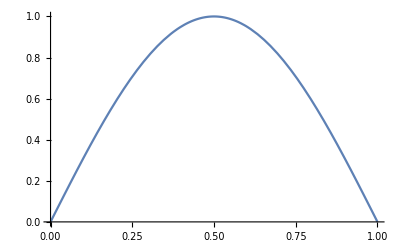

```mathematica
Plot[usol[x2,0],{x2,0,1}]
```

```mathematica
Plot3D[usol[x2,t2],{x2,0,1},{t2,0,1}]
```

-Graphics3D-

```mathematica
ContourPlot[usol[x1,t1],{x1,0,1},{t1,0,1},BaseStyle->FontSize->22,FrameLabel->{"x","t"},PlotLegends->Automatic,LabelStyle->FontSize->18,AspectRatio->1/4]
```

-Graphics-

```mathematica
Length[Table[i,{i,0,1,1/10}]]
```

11

```mathematica
For[gridres=10,gridres<110,gridres+=10,
grid=Table[t,{t,0,1,1/gridres}];
tab=Table[usol[x,t],{x,grid},{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","wave_sln_",ToString[gridres],".csv"],tab]
]
```